# Exploration of Noble Gases

Noble gases are located in the far right of the periodic table. They possess great stability and rarely react with other elements. Under standard conditions, they are all odorless, colorless, and monatomic gases.

## General properties of noble gases

Generate the list of noble gases:

```mathematica
class=EntityClass["Element", "NobleGas"]
```

noble gases

Find their abbreviations:

```mathematica
entities=class["Entity"];
abbs=class["Abbreviation"];
```

```mathematica
Thread[entities->abbs]
```

{helium→He,neon→Ne,argon→Ar,krypton→Kr,xenon→Xe,radon→Rn,oganesson→Og}

Locate them in white in the periodic table:

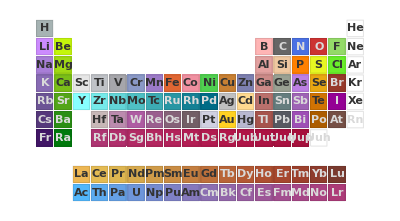

```mathematica
ColorData["Atoms","Image"]/.Thread[class["IconColor"]->White]
```

We consider a subset of noble gases for our analysis.

Construct a list of noble gases:

```mathematica
noblegases=CanonicalName[entities][[1;;4]]
```

{Helium,Neon,Argon,Krypton}

We analyze some of their properties:

Extract data using the Wolfram Language symbol ThermodynamicData:

```mathematica
properties=DeleteMissing[ThermodynamicData[#]]&/@noblegases;
```

Construct an array of properties:

```mathematica
data=Transpose[Join[{Keys[properties]⟦1⟧},Values/@properties]];
```

Display these properties in a grid:

```mathematica
Grid[Prepend[data⟦1;;6⟧,data⟦20⟧],Frame->All]
```

Name | helium | neon | argon | krypton
CriticalDensity | 69.6412 kg/m^3 | 481.915 kg/m^3 | 535.6 kg/m^3 | 909.208 kg/m^3
CriticalEnthalpy | 11869.8 J/kg | 59461. J/kg | -4331.55 J/kg | 76278.5 J/kg
CriticalEntropy | 2183.29 J/(kg K) | 1502.21 J/(kg K) | 2247.64 J/(kg K) | 424.449 J/(kg K)
CriticalInternalEnergy | 8619.35 J/kg | 53902.7 J/kg | -13411.1 J/kg | 70201.2 J/kg
CriticalPressure | 227460. Pa | 2.6786×10^6 Pa | 4.863×10^6 Pa | 5.525×10^6 Pa
CriticalTemperature | 5.1953 K | 44.4918 K | 150.687 K | 209.48 K

```mathematica
Grid[Prepend[data⟦7;;12⟧,data⟦20⟧],Frame->All]
```

Name | helium | neon | argon | krypton
Density | 0.166317 kg/m^3 | 0.838471 kg/m^3 | 1.66182 kg/m^3 | 3.49123 kg/m^3
Enthalpy | 1.52789×10^6 J/kg | 361621. J/kg | 152325. J/kg | 151069. J/kg
Entropy | 27879.3 J/(kg K) | 5661.71 J/(kg K) | 3864.12 J/(kg K) | 1122.6 J/(kg K)
InternalEnergy | 918658. J/kg | 240776. J/kg | 91353.2 J/kg | 122046. J/kg
IsobaricHeatCapacity | 5192.99 J/(kg K) | 1030.37 J/(kg K) | 521.608 J/(kg K) | 249.257 J/(kg K)
IsochoricHeatCapacity | 3116.03 J/(kg K) | 618.144 J/(kg K) | 312.398 J/(kg K) | 149.039 J/(kg K)

```mathematica
Grid[Prepend[data⟦13;;19⟧,data⟦20⟧],Frame->All]
```

Name | helium | neon | argon | krypton
MolarDensity | 41.5522 mol/m^3 | 41.5517 mol/m^3 | 41.5996 mol/m^3 | 41.6625 mol/m^3
MolarEnthalpy | 6115.52 J/mol | 7297.15 J/mol | 6085.1 J/mol | 12659.3 J/mol
MolarEntropy | 111.59 J/(K mol) | 114.248 J/(K mol) | 154.364 J/(K mol) | 94.0719 J/(K mol)
MolarInternalEnergy | 3677.02 J/mol | 4858.62 J/mol | 3649.38 J/mol | 10227.2 J/mol
MolarIsobaricHeatCapacity | 20.7855 J/(mol K) | 20.7918 J/(mol K) | 20.8372 J/(mol K) | 20.8872 J/(mol K)
MolarIsochoricHeatCapacity | 12.4722 J/(mol K) | 12.4735 J/(mol K) | 12.4797 J/(mol K) | 12.4892 J/(mol K)
MolarSpecificVolume | 0.0240661 m^3/kg | 0.0240664 m^3/kg | 0.0240387 m^3/kg | 0.0240024 m^3/kg

```mathematica
Grid[Prepend[data⟦22;;25⟧,data⟦20⟧],Frame->All]
```

Name | helium | neon | argon | krypton
SoundSpeed | 1007.86 m/s | 448.922 m/s | 318.959 m/s | 220.072 m/s
SpecificVolume | 6.01262 m^3/kg | 1.19265 m^3/kg | 0.60175 m^3/kg | 0.286432 m^3/kg
ThermalConductivity | 0.153505 W/(m K) | 0.0475569 W/(m K) | 0.0174963 W/(m K) | 0.00922286 W/(m K)
TriplePointGasDensity | 1.14551 kg/m^3 | 4.44453 kg/m^3 | 4.05458 kg/m^3 | 6.57099 kg/m^3

```mathematica
Grid[Prepend[data⟦26;;All⟧,data⟦20⟧],Frame->All]
```

Name | helium | neon | argon | krypton
TriplePointLiquidDensity | 146.242 kg/m^3 | 1252.28 kg/m^3 | 1416.75 kg/m^3 | 2446.9 kg/m^3
TriplePointPressure | 4856.5 Pa | 43464. Pa | 68891. Pa | 73500. Pa
TriplePointTemperature | 2.1768 K | 24.556 K | 83.8058 K | 115.775 K
Viscosity | 0.0000196176 s Pa | 0.0000307712 s Pa | 0.0000223065 s Pa | 0.0000247551 s Pa

## Analysing density functions

Let us analyse the density of the noble gases with respect to pressure and temperature.

Construct the density data for a constant temperature of 50°C:

```mathematica
densitydata=Transpose[
{Quantity[1000Range[1,100,2],"Pascals"],ThermodynamicData[#,"Density",{"Temperature"->Quantity[50,"DegreesCelsius"],"Pressure"->Quantity[Range[1,100,2]1000,"Pascals"]}]
}]&/@noblegases;
```

Plot the density function:

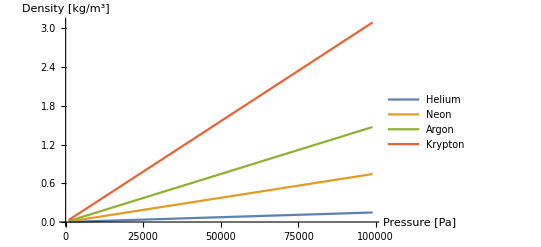

```mathematica
ListLinePlot[densitydata,
AxesLabel->{"Pressure [Pa]","Density [kg/m^3]"},
PlotLegends->noblegases]
```

Let us do the same with a constant atmospheric pressure.

Construct the density data for a constant pressure of 20 Pa:

```mathematica
densitydata2=Transpose[
{Quantity[Range[100,400,10],"Kelvins"],
ThermodynamicData[#,"Density",{"Pressure"->Quantity[20,"Pascals"],"Temperature"->Quantity[Range[100,400,10],"Kelvins"]}]
}]&/@noblegases;
```

Plot the pressure function:

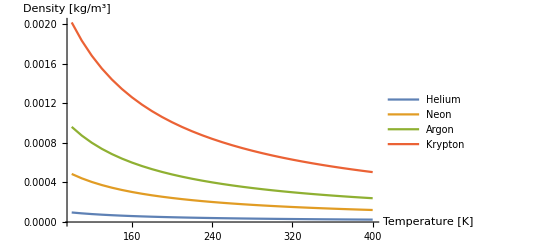

```mathematica
ListLinePlot[densitydata2,
AxesLabel->{"Temperature [K]","Density [kg/m^3]"},
PlotLegends->noblegases]
```

The shapes of the density functions are similar. We can also see that they are continuous, which indicate that for the selected range of temperature, no phase transition happens.

## Phase plotting

Let us build the phase plots of each noble gas.

Choose the pressure interval:

```mathematica
pressures=Quantity[Table[10^x,{x,-6,12,0.3}],"Pascals"];
```

Create a phase plot for each noble gas:

```mathematica
phaseplots=ListLogPlot[
Transpose[
{#,pressures}
]&
/@
{ThermodynamicData[#,"LiquidVaporPhaseBoundary",{"Pressure"->pressures}],
ThermodynamicData[#,"SolidLiquidPhaseBoundary",{"Pressure"->pressures}],
ThermodynamicData[#,"SolidVaporPhaseBoundary",{"Pressure"->pressures}]},
PlotRange->All,
Joined->True,
Frame->True,
FrameLabel->{"Temperature [K]","Pressure [Pa]"},
PlotLegends->{"Vapor Liquid","Solid Liquid","Solid Vapor"},
GridLines->Automatic,
PlotLabel->#,
ImageSize->Medium]&/@noblegases;
```

Display these plots in a grid:

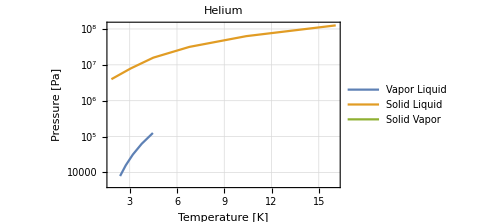
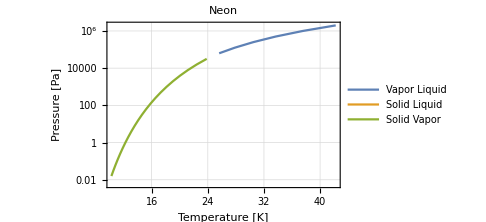
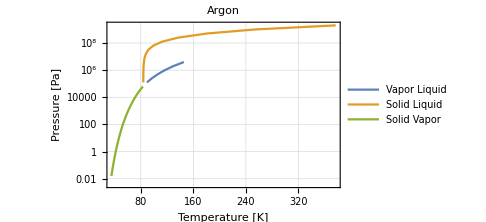
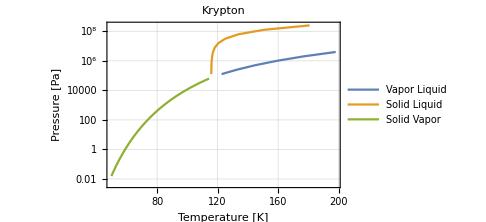
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[Partition[phaseplots,2],Spacings->{5,5}]
```

## Phase plot analysing

Let us analyse the vapor-liquid phase boundary.

Construct the array of data near the vapor-liquid boundary with constant pressure:

```mathematica
dataTemp=Transpose[{Quantity[Table[x,{x,1,200,10}],"Kelvins"],ThermodynamicData[#,"Density",{"Temperature"->Quantity[Table[x,{x,1,200,10}],"Kelvins"],"Pressure"->Quantity[10^6,"Pascals"]}]}]&/@noblegases;
```

Construct the array of data near the vapor-liquid boundary with constant temperature:

```mathematica
dataPress=Transpose[{Quantity[Table[10^5*i,{i,1,10}],"Pascals"],ThermodynamicData[#,"Density",{"Temperature"->Quantity[200,"Kelvins"],"Pressure"->Quantity[Table[10^i,{i,1,10}],"Pascals"]}]}]&/@noblegases;
```

Display the data in a grid:

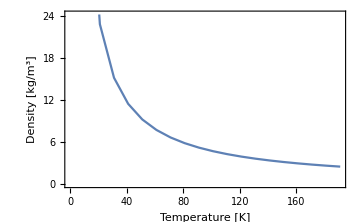
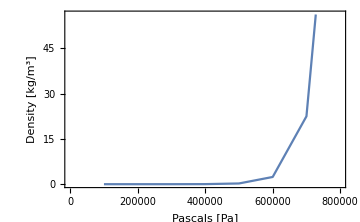
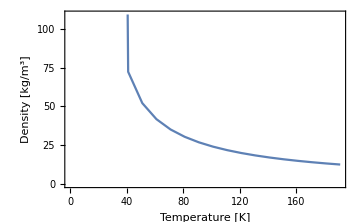
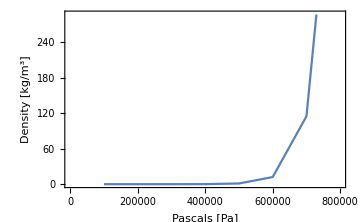
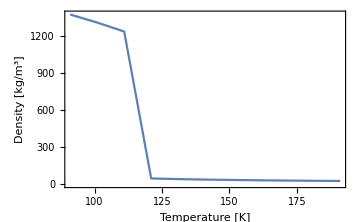
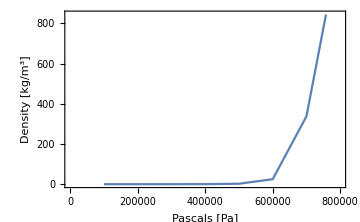
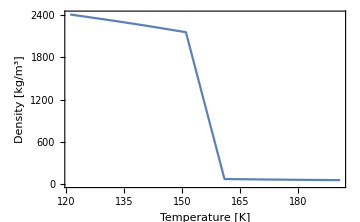
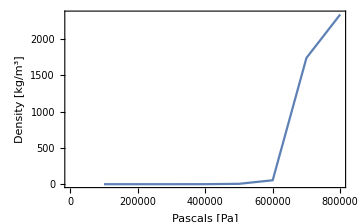
Helium | -Graphics- | -Graphics-
Neon | -Graphics- | -Graphics-
Argon | -Graphics- | -Graphics-
Krypton | -Graphics- | -Graphics-

```mathematica
Grid[Table[{noblegases[[i]],ListLinePlot[dataTemp[[i]],Axes->False,Frame->True,FrameLabel->{"Temperature [K]","Density [kg/m^3]"},ImageSize->Medium],ListLinePlot[dataPress[[i]],Axes->False,Frame->True,FrameLabel->{"Pascals [Pa]","Density [kg/m^3]"},ImageSize->Medium]},{i,1,Length[noblegases]}]]
```

We can see discontinuities in the density functions for low temperatures. This is an indication of the process of vapor-liquid phase transition of the noble gases.

Further Explorations

Analysing of other kinds of gases like halogens

Analysing of another properties of substances

Authorship information

Andrey Krotkikh

6/21/2017

andrei.krotkih@gmail.com